## Calculus

Mathematica is an efficient tool that can analytically or numerically differentiate, integrate, and solve differential equations.

### Differentiation

```mathematica
D[Log[x],x]
D[x^3+1/x,x]
D[BesselJ[4,x],x]
```

```mathematica
D[(a x^2+b x-1)/(x+γ Sin[x]),x]
```

```mathematica
D[(a x^2+b x-1)/(x+γ Sin[x]),x]//FullSimplify
```

```mathematica
Integration
```

```mathematica
Integrate[Log[x],x]
Integrate[Tan[x]+Sin[x],x]
```

```mathematica
Integrate[(k Q x)/((x^2 + y^2)^(3/2)),y]
Integrate[(k Q x)/((x^2 + y^2)^(3/2)),{y,-a,a}]
```

### Differential Equations

You can solve differential equations analytically or numerically. Look at the solution to Bessel’s equation, which appears in various physical phenomena from diffraction from helical objects like DNA to vibrational modes of circular acoustic membranes (drums!)

```mathematica
solB = DSolve[x^2 y''[x]+x y'[x] + (x^2-2^2)y[x]==0,y[x],x]
```

```mathematica
solBs = DSolve[{x^2 y''[x]+x y'[x] + (x^2-2^2)y[x]==0,y[0]==1,y'[0]==0},y[x],x]
```

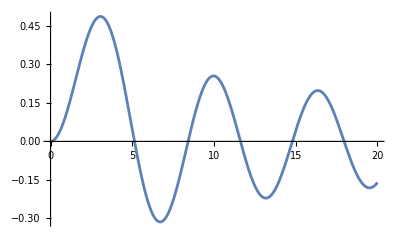

```mathematica
Plot[y[x]/.solB/.{C[1]->1,C[2]->0},{x,0,20}]
```

Not all differential equations will have a analytic solution. The Endem-Chardrasekhar equation describes the density distribution of a spherically symmetric isothermal gas sphere subjected to its own gravitational force. Under isothermal assumptions, this can model the core of a star

```mathematica
ecequ = NDSolve[{y''[x]+2/x y'[x]==Exp[-y[x]],y[ϵ]==0,y'[ϵ]==0},y[x],{x,ϵ,30}]
```

```mathematica
Plot[y[x]/.ecequ,{x,ϵ,10},AxesLabel->{"x","y"}]
```

```mathematica
Plot[Exp[-y[x]]/.ecequ,{x,ϵ,10},AxesLabel->{"ξ","ρ/ρ_c"}]
```

where ξ = r √(4π G ρ_c W m_p/k_bT)

## Functions

The most useful aspect of Mathematica is defining functions. Functions are mathematical processes that relate a set of values X to another set of values Y. 
There are 3 distinct ways of defining a function in Mathematica. All get the job done, but I prefer the last syntax.

```mathematica
f = Function[{x,y},x^2+y^2];
g = (#1^2+#2^2) &;
h[x_,y_] := x^2+y^2;
f[2,3]
g[2,3]
h[2,3]
```

```mathematica
x
```

Example Functions

You can use your function just like any other in Mathematica. Let’s take a look at the normal distribution

```mathematica
normal[μ_,σ_,x_]:=1/(√(2π σ^2))Exp[(-(x-μ)^2)/(2 σ^2)];
```

```mathematica
Plot[normal[-9,10,x],{x,-37,10},PlotRange->{0,0.05}]
```

```mathematica
Manipulate[Plot[normal[mean,var,x],{x,mean-4var,mean+4var}],{mean,-10,10},{var,0.1,10}]
```

```mathematica
Manipulate[Plot[normal[mean,var,x],{x,mean-5 var,mean+5 var},PlotRange->{0,1}],{mean,-9,9},{var,0.1,10}]
```

```mathematica
G[μ_,σ_,lim_]:= Integrate[normal[μ,σ,x],{x,μ-lim,μ+lim}]
```

```mathematica
G[0,8,16]//N
```

```mathematica
Plot[G[4,1,y],{y,0,4}]
```

You can define convenience functions:

```mathematica
Quad[a_,b_,c_] := NSolve[a x^2 + b x + c==0,x]
Tri[a_,b_,c_,d_] :=NSolve[a x^3 + b x^2 + c x +d==0,x]
```

```mathematica
Quad[2,7,1]
First[Quad[2,7,1]][[1,1]]
```

```mathematica
Log[x]/.Quad[2,7,1][[2]]
```

```mathematica
trisol = Flatten[Tri[2,4,-7,4]]
```

```mathematica
trisol[[1,2]]
```

## Modules

Mathematica allows you to write your own multi-line functions (called modules in Wolfram language). Modules allow you to define local variables, combine code statements, and return values. Some examples are below.

Writing Euclid’s algorithm for the GCD (as seen in Wolfram Documentation):

```mathematica
gcd[m0_,n0_] := Module[{m=m0,n=n0},While[n ≠ 0, {m,n}={n,Mod[m,n]}];m]
```

```mathematica
gcd[1800,3645]
```

You can functions to calculate projectile motion calculations:

```mathematica
moonProj[v_,θ_,h_] :=Module[{g=1.6,th=π*θ/180}, R = (v^2 Cos[th] Sin[th])/g+√((v^4 Cos[th]^2 Sin[th]^2)/g^2+(2 h v^2 Cos[th]^2)/g); 
vf = √(v^2+2*g*h);
time= v/g Sin[th]+√(v^2/g^2 Sin[th]+2 h/g); Return[{R,time,vf}]];
```

```mathematica
moonProj[40,60,9]
```

## Partial Differential Equations

Let’s look at defining functions from analytical solutions to differential equations. You would like to do this to graph the solutions in interesting ways. Let’s look the 2D radial wave equation.

```mathematica
eqn=r D[u[r,t],{t,2}]==D[r D[u[r,t],r],r];
dsol=DSolve[{eqn, u[1,t]==0,u[r,0]==0,Derivative[0,1][u][r,0]==1},u[r,t],{r,t}]
```

{{u[r,t]→(2 BesselJ[0,r BesselJZero[0,K[1]]] BesselJ[1,BesselJZero[0,K[1]]] Sin[t BesselJZero[0,K[1]]])/((BesselJ[0,BesselJZero[0,K[1]]]^2+BesselJ[1,BesselJZero[0,K[1]]]^2) BesselJZero[0,K[1]]^2)K[1]1∞}}

```mathematica
h[r_,t_]=u[r,t]/. dsol[[1]]/. {∞->3}//Activate//N
```

```mathematica
Manipulate[Plot3D[Evaluate[h[Sqrt[x^2+y^2],t]],{x,-1,1},{y,-1,1},PlotRange->{-1,1},Ticks->None,Mesh->True,PlotStyle->Yellow,Boxed->False,Axes->False,ImageSize->Medium,AspectRatio->1],{t,0,10.45,0.05}]
```

Google Gemini produced an alternative for me that makes the membrane explicitly circular

```mathematica
ListAnimate[Table[Plot3D[Evaluate[h[r,t]/. {r->Sqrt[x^2+y^2]}],{x,y}∈Disk[],PlotRange->{-1,1},Ticks->None,Mesh->True,MeshStyle->{Red,Blue},PlotStyle->Yellow,Boxed->False,Axes->False,ImageSize->Medium,AspectRatio->1,Background->Lighter[Orange,0.85]],{t,0,10.45,0.05}]]
```